```mathematica
Quit[];
```

```mathematica
mmu=MaxMemoryUsed[]
SetDirectory[NotebookDirectory[]];
(* Global Properties *)
eV=27.211;
h=4.135667516×10^-15;
c=3×10^8;
shell={"s","p","p+","d","d+","f","f+","g","g+"};
RelOrbitals={"4s","5s","4p","4p+","5p","5p+","4d","4d+","5d","5d+","4f","4f+","5f","5f+","5g","5g+"};
jOrbitals={0.5,0.5,0.5,1.5,0.5,1.5,1.5,2.5,1.5,2.5,2.5,3.5,2.5,3.5,3.5,4.5};
(* s must ne first; nj, nj+ must be consecutive *) 
NonRelOrbitals={"4s","5s","4p","5p","4d","5d","4f","5f","5g"};
l={0,0,1,1,2,2,3,3,4};
MaxElectrons=2(2l+1);
spin={0.5,-0.5};

<<ReadAMBiTOutput`;
<<MBQCSpectra`;

FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=600; (* Export Image Resolution dpi *)
```

85018888

```mathematica
(* Sn08 -> 15, Sn09 -> 16, Sn10 -> 17, Sn11 -> 20, Sn12 -> 22, Sn13 -> 23, Sn14 -> 24*)
SpreadWidth={16,17,20,22,23,24};
Ions={"09","10","11","12","13","14"};
con={"df-df-df-0","df-df-df-0","df-df-df-0","df-df-df-0","df-df-df-0","df-df-d-0"};
PhotonMBQC ={};
PhotonNoCI={};
PhotonCI={};
IntMBQC={};
IntNoCI={};
IntCI={};
SpecMBQC={};
SpecNoCI={};
SpecCI={};

For[ind=1,ind≤6,ind++,
{
Print[ind];
ION=Ions[[ind]];
configs=con[[ind]];
filenameMBQC="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileMBQC=Import[filenameMBQC,"CSV"];
filenameCI="E1_Transitions3/Sn"<>ION<>"/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileCI=Import[filenameCI,"CSV"];
filename0diag="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
file0diag=(*Import[filename0diag,"CSV"];*)fileMBQC;
Print["Files Loaded"];
{Shells,EnergyCSF,Num}=ReadLevels[fileMBQC];
L=Length[Shells];
TotalLines=L*(L-1)/2;
EnergyCSF=EnergyCSF eV;

NumTotal=Total[Num];
T=SingleTransitionData[fileMBQC];
Ltran=Length[T];

G=SpreadWidth[[ind]];
Cutoff=G; (*Lorenzian has range 2*Cutoff *)
Temp=26;
increment=0.005;
max=Max[EnergyCSF]+Cutoff+10;
min=Floor[Min[EnergyCSF]-Cutoff-10];
{z,Density}=LevelDensity[EnergyCSF,Num,G,increment,max,min,Cutoff];


{Emin,PsiE}=ComplexWaveEnergies[G,z,Density,increment,EnergyCSF,Num];
PsiE=PsiE-Emin;
z=z-Emin;
EnergyCSF=EnergyCSF-Emin;

Components=ComplexCoefficients2[G,EnergyCSF,Num,2*Cutoff];
Components2=Components^2;
Dspacing=Table[LevelSpacing3[PsiE,EnergyCSF[[i]],G],{i,1,L}];

{CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs}=NonRelativisticConfiguration[Shells,Num];

AverageJ=ConigurationAverageJ[CONFIGS];
AverageJall=ConstantArray[0,Length[NonRelConfigs]];
For[i=1,i≤Length[CONFIGS],i=i+1,
{
pos=Position[NonRelConfigs,CONFIGS[[i]]];
AverageJall[[posᵀ[[1]]]]=AverageJ[[i]];
}];

Jinitial=Table[Total[AverageJall*Components[[i]]]/Total[Components[[i]]],{i,1,L}];

nAverage=(RelConfigsᵀ/(2*jOrbitals+1))ᵀ;
Z=Total[Table[Num[[i]]*Exp[-EnergyCSF[[i]]/Temp],{i,1,L}]];

Print["Configurations Calculated"];

E1=Table[E1Transitions[i,j,Shells,T,nAverage],{i,1,L},{j,1,L}];
indicies=ListIndicies[L];

Shift=0;

(* iPsi lower energy then jPsi *)
(* jPsi -> iPsi *)
Tic=AbsoluteTime[];
Efinal=EnergyCSF[[indicies[[1]]]];
Dspacing2=Dspacing[[indicies[[1]]]];
Einitial=EnergyCSF[[indicies[[2]]]];
Light=Einitial-Efinal+Shift;
Jin=Jinitial[[indicies[[2]]]];
NumLines=Num[[indicies[[1]]]]*Num[[indicies[[2]]]];

Cutoff=40;
Renorm=2/π*ArcTan[Cutoff/G];
StrengthNorm=Table[Main[i,Cutoff,Renorm,G,T,Light,indicies,Dspacing2,Jin,NumLines,E1,Ltran,Components2],
{i,1,TotalLines}];

Einstein=(2.0261*10^18)*(Light)^3/(4.1357*10^-15*3*10^8*10^10)^3 *StrengthNorm;
Intensity=Exp[-Einitial/Temp]*Einstein*Light/(4π Z);


Toc=AbsoluteTime[];
Print["Done MBQC, Time Taken: ",Toc-Tic];

{ECI,SCI,EINITIAL,EFINAL,IntensityCI,EinsteinCI}=DiscreteLevels[fileCI,Temp,Emin];
{Ediag,Sdiag,EINITIALdiag,EFINALdiag,Intensitydiag,Einsteindiag}=DiscreteLevels[file0diag,Temp,Emin];
Print["AMBiT Calculated"];

spread=1;
EnergyRange=Range[0,300,0.1];

(*MBQCSpectrum=DiscreteSpectrum[Light,StrengthNorm,EnergyRange,spread];
CISpectrum=DiscreteSpectrum[ECI,SCI,EnergyRange,spread];
Diag0Spectrum=DiscreteSpectrum[Ediag,Sdiag,EnergyRange,spread];
MBQCEinstein=DiscreteSpectrum[Light,Einstein,EnergyRange,spread];
CIEinstein=DiscreteSpectrum[ECI,EinsteinCI,EnergyRange,spread];
Diag0Einstein=DiscreteSpectrum[Ediag,Einsteindiag,EnergyRange,spread];*)
MBQCIntensity=DiscreteSpectrum[Light,Intensity,EnergyRange,spread];
CIIntensity=DiscreteSpectrum[ECI,IntensityCI,EnergyRange,spread];
Diag0Intensity=DiscreteSpectrum[Ediag,Intensitydiag,EnergyRange,spread];

Print["Spectra Calculates"];

AppendTo[PhotonMBQC,Light];
AppendTo[PhotonNoCI,Ediag];
AppendTo[PhotonCI,ECI];
AppendTo[IntMBQC,Intensity];
AppendTo[IntNoCI,Intensitydiag];
AppendTo[IntCI,IntensityCI];
AppendTo[SpecMBQC,MBQCIntensity];
AppendTo[SpecNoCI,Diag0Intensity];
AppendTo[SpecCI,CIIntensity];

Print[" "];
}]
```

1

Files Loaded

Configurations Calculated

Done MBQC, Time Taken: 541.079582

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

2

Files Loaded

Error i=79513 last=-4704.25

Configurations Calculated

Done MBQC, Time Taken: 558.1172879

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

5

Files Loaded

Configurations Calculated

Done MBQC, Time Taken: 178.627843

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

6

Files Loaded

Configurations Calculated

Done MBQC, Time Taken: 45.384071

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

Done MBQC, Time Taken: 539.2489007

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

3

Files Loaded

Error i=64171 last=-4492.88

Configurations Calculated

Done MBQC, Time Taken: 955.8230832

AMBiT Calculated

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Spectra Calculates

4

Files Loaded

Error i=38076 last=-4259.2

Configurations Calculated

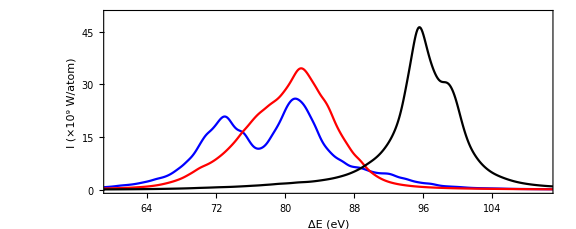

```mathematica
AR=1/2.5;

axis={{60,110},{0,50}};

Frac={0,0.013,0.103,0.374,0.396,0.114};
SpectrumMBQC=Frac.SpecMBQC;
SpectrumCI=Frac.SpecCI;
SpectrumNoCI=Frac.SpecNoCI;

im1=ListLinePlot[{EnergyRange,SpectrumMBQC/10^9}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
im2=ListLinePlot[{EnergyRange,SpectrumNoCI/10^9}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
im3=ListLinePlot[{EnergyRange,SpectrumCI/10^9}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
Show[{im1,im2,im3},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ΔE (eV)","I (×10^9 W/atom)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
```